## Write down the nondimensionalized Fokker-Planck equation

```mathematica
FP= D[p[t, xt, yt], t]==λt*D[yt*p[t, xt, yt], xt]+D[yt*p[t, xt, yt], yt]-D[xt*p[t, xt, yt],yt]
```

p^(1,0,0)[t,xt,yt]==p[t,xt,yt]-xt p^(0,0,1)[t,xt,yt]+yt p^(0,0,1)[t,xt,yt]+yt λt p^(0,1,0)[t,xt,yt]

## Get the steady-state variances

```mathematica
A= {{ 0,λt},{-1, 1}}
B = {{αt,0},{0,αt}}
s=Array[Y,{2,2}]
ss =( s/. Expand[FullSimplify[Solve[A.s+s.Transpose[A]==B.Transpose[B], Flatten[s]]]])[[1]]
```

{{0,λt},{-1,1}}

{{αt,0},{0,αt}}

{{Y[1,1],Y[1,2]},{Y[2,1],Y[2,2]}}

{{αt^2/2+αt^2/(2 λt)+(αt^2 λt)/2,αt^2/(2 λt)},{αt^2/(2 λt),αt^2/2+αt^2/(2 λt)}}

```mathematica
FullSimplify[MatrixExp[-A*t].{{x0, xy0}, {xy0, y0}}.MatrixExp[-Transpose[A]*t]]
```

{{1/(-1+4 λt)(-Cosh[t]+Sinh[t]) (-2 λt (x0-xy0+y0 λt)+(x0-2 (x0+xy0) λt+2 y0 λt^2) Cosh[t √(1-4 λt)]+√(1-4 λt) (x0-2 xy0 λt) Sinh[t √(1-4 λt)]),(ⅇ^-t (x0-xy0+y0 λt-(x0+(-4 xy0+y0) λt) Cosh[t √(1-4 λt)]+√(1-4 λt) (-x0+y0 λt) Sinh[t √(1-4 λt)]))/(-1+4 λt)},{(ⅇ^-t (x0-xy0+y0 λt-(x0+(-4 xy0+y0) λt) Cosh[t √(1-4 λt)]+√(1-4 λt) (-x0+y0 λt) Sinh[t √(1-4 λt)]))/(-1+4 λt),1/(2 (-1+4 λt))ⅇ^(-t (1+√(1-4 λt))) (-2 (-1+ⅇ^(t √(1-4 λt)))^2 x0+2 ⅇ^(t √(1-4 λt)) (-2 xy0+2 y0 λt+(2 xy0+y0 (-1+2 λt)) Cosh[t √(1-4 λt)]+(-2 xy0+y0) √(1-4 λt) Sinh[t √(1-4 λt)]))}}

```mathematica
Series[%1358, {λt, 0, 1}]
```

{{(Cosh[t]-Sinh[t]) (x0 Cosh[t]+x0 Sinh[t])-2 ((Cosh[t]-Sinh[t]) (x0-xy0-x0 Cosh[t]+t x0 Cosh[t]+xy0 Cosh[t]-x0 Sinh[t]+t x0 Sinh[t]+xy0 Sinh[t])) λt+O[λt]^2,ⅇ^-t (-x0+xy0+x0 Cosh[t]+x0 Sinh[t])-ⅇ^-t (4 x0-4 xy0+y0-4 x0 Cosh[t]+2 t x0 Cosh[t]+4 xy0 Cosh[t]-y0 Cosh[t]-2 x0 Sinh[t]+2 t x0 Sinh[t]+y0 Sinh[t]) λt+O[λt]^2},{ⅇ^-t (-x0+xy0+x0 Cosh[t]+x0 Sinh[t])-ⅇ^-t (4 x0-4 xy0+y0-4 x0 Cosh[t]+2 t x0 Cosh[t]+4 xy0 Cosh[t]-y0 Cosh[t]-2 x0 Sinh[t]+2 t x0 Sinh[t]+y0 Sinh[t]) λt+O[λt]^2,-1/2 ⅇ^(-2 t) (-2 (-1+ⅇ^t)^2 x0+2 ⅇ^t (-2 xy0+(2 xy0-y0) Cosh[t]+(-2 xy0+y0) Sinh[t]))+1/2 (-4 ⅇ^-t (-2 t x0+2 ⅇ^t t x0+2 t xy0+y0+y0 Cosh[t]+2 xy0 Sinh[t]-y0 Sinh[t])+(-4 ⅇ^(-2 t)-2 ⅇ^(-2 t) t) (-2 (-1+ⅇ^t)^2 x0+2 ⅇ^t (-2 xy0+(2 xy0-y0) Cosh[t]+(-2 xy0+y0) Sinh[t]))) λt+O[λt]^2}}

```mathematica
FullSimplify[%]
```

{{x0-2 ((-1+t) x0+ⅇ^-t (x0-xy0)+xy0) λt+O[λt]^2,ⅇ^-t ((-1+ⅇ^t) x0+xy0)+(3 x0-2 t x0-2 xy0-ⅇ^-t (4 x0-4 xy0+y0)+ⅇ^(-2 t) (x0-2 xy0+y0)) λt+O[λt]^2},{ⅇ^-t ((-1+ⅇ^t) x0+xy0)+(3 x0-2 t x0-2 xy0-ⅇ^-t (4 x0-4 xy0+y0)+ⅇ^(-2 t) (x0-2 xy0+y0)) λt+O[λt]^2,ⅇ^(-2 t) ((-1+ⅇ^t)^2 x0+2 (-1+ⅇ^t) xy0+y0)-2 (ⅇ^(-2 t) ((-1+ⅇ^t) (2+ⅇ^t (-2+t)+t) x0+(3+ⅇ^t (-4+ⅇ^t)+2 t) xy0+(-1+ⅇ^t-t) y0)) λt+O[λt]^2}}

```mathematica
Expand[%]
```

{{x0-2 ((-1+t) x0+ⅇ^-t (x0-xy0)+xy0) λt+O[λt]^2,ⅇ^-t ((-1+ⅇ^t) x0+xy0)+(3 x0-2 t x0-2 xy0-ⅇ^-t (4 x0-4 xy0+y0)+ⅇ^(-2 t) (x0-2 xy0+y0)) λt+O[λt]^2},{ⅇ^-t ((-1+ⅇ^t) x0+xy0)+(3 x0-2 t x0-2 xy0-ⅇ^-t (4 x0-4 xy0+y0)+ⅇ^(-2 t) (x0-2 xy0+y0)) λt+O[λt]^2,ⅇ^(-2 t) ((-1+ⅇ^t)^2 x0+2 (-1+ⅇ^t) xy0+y0)-2 (ⅇ^(-2 t) ((-1+ⅇ^t) (2+ⅇ^t (-2+t)+t) x0+(3+ⅇ^t (-4+ⅇ^t)+2 t) xy0+(-1+ⅇ^t-t) y0)) λt+O[λt]^2}}

```mathematica
Collect[%, {x0, xy0, y0}]
```

{{xy0 (-2 λt+2 ⅇ^-t λt)+x0 (1+2 λt-2 ⅇ^-t λt-2 t λt),y0 (ⅇ^(-2 t) λt-ⅇ^-t λt)+xy0 (ⅇ^-t-2 λt-2 ⅇ^(-2 t) λt+4 ⅇ^-t λt)+x0 (1-ⅇ^-t+3 λt+ⅇ^(-2 t) λt-4 ⅇ^-t λt-2 t λt)},{y0 (ⅇ^(-2 t) λt-ⅇ^-t λt)+xy0 (ⅇ^-t-2 λt-2 ⅇ^(-2 t) λt+4 ⅇ^-t λt)+x0 (1-ⅇ^-t+3 λt+ⅇ^(-2 t) λt-4 ⅇ^-t λt-2 t λt),xy0 (-2 ⅇ^(-2 t)+2 ⅇ^-t-2 λt-6 ⅇ^(-2 t) λt+8 ⅇ^-t λt-4 ⅇ^(-2 t) t λt)+y0 (ⅇ^(-2 t)+2 ⅇ^(-2 t) λt-2 ⅇ^-t λt+2 ⅇ^(-2 t) t λt)+x0 (1+ⅇ^(-2 t)-2 ⅇ^-t+4 λt+4 ⅇ^(-2 t) λt-8 ⅇ^-t λt-2 t λt+2 ⅇ^(-2 t) t λt)}}

## Choose the parameter values

```mathematica
λts = {0.02,0.05, 0.1, 0.15,0.24};
αts = {0.3, 0.4, 0.5, 0.6, 0.7};
tfs = Flatten[Transpose[Table[5/λts, 5]]]
αArray2 = Flatten[Table[{0.3, 0.4, 0.5, 0.6, 0.7},5]]^2
params = Flatten[Table[{λt->l, αt->a}, {l, λts}, {a, αts}], 1]
legend =  Flatten[Table["λt="<>ToString[l]<>"; "<> "αt="<>ToString[a], {l, λts},{a, αts}], 1];
```

{250.,250.,250.,250.,250.,100.,100.,100.,100.,100.,50.,50.,50.,50.,50.,33.3333,33.3333,33.3333,33.3333,33.3333,20.8333,20.8333,20.8333,20.8333,20.8333}

{0.09,0.16,0.25,0.36,0.49,0.09,0.16,0.25,0.36,0.49,0.09,0.16,0.25,0.36,0.49,0.09,0.16,0.25,0.36,0.49,0.09,0.16,0.25,0.36,0.49}

{{λt→0.02,αt→0.3},{λt→0.02,αt→0.4},{λt→0.02,αt→0.5},{λt→0.02,αt→0.6},{λt→0.02,αt→0.7},{λt→0.05,αt→0.3},{λt→0.05,αt→0.4},{λt→0.05,αt→0.5},{λt→0.05,αt→0.6},{λt→0.05,αt→0.7},{λt→0.1,αt→0.3},{λt→0.1,αt→0.4},{λt→0.1,αt→0.5},{λt→0.1,αt→0.6},{λt→0.1,αt→0.7},{λt→0.15,αt→0.3},{λt→0.15,αt→0.4},{λt→0.15,αt→0.5},{λt→0.15,αt→0.6},{λt→0.15,αt→0.7},{λt→0.24,αt→0.3},{λt→0.24,αt→0.4},{λt→0.24,αt→0.5},{λt→0.24,αt→0.6},{λt→0.24,αt→0.7}}

## Get the trajectory of the mean

```mathematica
eig=FullSimplify[Eigenvectors[A]]
```

{{1/2 (1+√(1-4 λt)),1},{1/2 (1-√(1-4 λt)),1}}

```mathematica
Eigenvalues[A]
```

{1/2 (1-√(1-4 λt)),1/2 (1+√(1-4 λt))}

```mathematica
cstar =Re[N[ Flatten[Table[(eig[[1,1]])^-1/.p, {p, params}]]]]
```

{1.02084,1.02084,1.02084,1.02084,1.02084,1.05573,1.05573,1.05573,1.05573,1.05573,1.12702,1.12702,1.12702,1.12702,1.12702,1.22515,1.22515,1.22515,1.22515,1.22515,1.66667,1.66667,1.66667,1.66667,1.66667}

## Set up the mesh, boundary conditions, and initial condition

#### Steady-state distribution widths in x~, y~

```mathematica
xtwidths = N[Table[ss[[1,1]]/.p, {p, params}]];
ytwidths = N[Table[ss[[2,2]]/.p, {p, params}]];
xtStds =Sqrt[xtwidths]
ytStds = Sqrt[ytwidths]
```

{1.51522,2.0203,2.52537,3.03045,3.53552,0.973268,1.29769,1.62211,1.94654,2.27096,0.706753,0.942338,1.17792,1.41351,1.64909,0.593085,0.79078,0.988475,1.18617,1.38387,0.493254,0.657673,0.822091,0.986509,1.15093}

{1.51493,2.0199,2.52488,3.02985,3.53483,0.972111,1.29615,1.62019,1.94422,2.26826,0.703562,0.938083,1.1726,1.40712,1.64165,0.587367,0.783156,0.978945,1.17473,1.37052,0.482183,0.64291,0.803638,0.964365,1.12509}

```mathematica
deltaWidth = 4;
deltaVar = deltaWidth^2
minCell = 0.05
```

16

0.05

```mathematica
Sqrt[αts[[1]]^2/2]
```

0.212132

#### Boundary condition at x~* =1. Choose the boundaries to be far enough away from the initial condition and the final distribution

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
xt0 = 12;
yt0 = xt0*cstar;
xtls=1-5*Sqrt[αArray2]
xtrs = xt0+5*xtStds
ytls=cstar
ytrs = cstar*xt0+5*ytStds
```

{-0.5,-1.,-1.5,-2.,-2.5,-0.5,-1.,-1.5,-2.,-2.5,-0.5,-1.,-1.5,-2.,-2.5,-0.5,-1.,-1.5,-2.,-2.5,-0.5,-1.,-1.5,-2.,-2.5}

{19.5761,22.1015,24.6269,27.1522,29.6776,16.8663,18.4885,20.1106,21.7327,23.3548,15.5338,16.7117,17.8896,19.0675,20.2455,14.9654,15.9539,16.9424,17.9309,18.9193,14.4663,15.2884,16.1105,16.9325,17.7546}

{1.02084,1.02084,1.02084,1.02084,1.02084,1.05573,1.05573,1.05573,1.05573,1.05573,1.12702,1.12702,1.12702,1.12702,1.12702,1.22515,1.22515,1.22515,1.22515,1.22515,1.66667,1.66667,1.66667,1.66667,1.66667}

{19.8247,22.3496,24.8745,27.3994,29.9242,17.5293,19.1495,20.7697,22.3898,24.01,17.042,18.2146,19.3872,20.5598,21.7324,17.6386,18.6176,19.5965,20.5754,21.5544,22.4109,23.2146,24.0182,24.8218,25.6255}

{{12,12.2501},{12,12.2501},{12,12.2501},{12,12.2501},{12,12.2501},{12,12.6687},{12,12.6687},{12,12.6687},{12,12.6687},{12,12.6687},{12,13.5242},{12,13.5242},{12,13.5242},{12,13.5242},{12,13.5242},{12,14.7018},{12,14.7018},{12,14.7018},{12,14.7018},{12,14.7018},{12,20.},{12,20.},{12,20.},{12,20.},{12,20.}}

{{16,0},{0,16}}

{{4,0},{0,4}}

{ImplicitRegion[-0.5≤xt≤19.5761&&1.02084≤yt≤19.8247,{xt,yt}],ImplicitRegion[-1.≤xt≤22.1015&&1.02084≤yt≤22.3496,{xt,yt}],ImplicitRegion[-1.5≤xt≤24.6269&&1.02084≤yt≤24.8745,{xt,yt}],ImplicitRegion[-2.≤xt≤27.1522&&1.02084≤yt≤27.3994,{xt,yt}],ImplicitRegion[-2.5≤xt≤29.6776&&1.02084≤yt≤29.9242,{xt,yt}],ImplicitRegion[-0.5≤xt≤16.8663&&1.05573≤yt≤17.5293,{xt,yt}],ImplicitRegion[-1.≤xt≤18.4885&&1.05573≤yt≤19.1495,{xt,yt}],ImplicitRegion[-1.5≤xt≤20.1106&&1.05573≤yt≤20.7697,{xt,yt}],ImplicitRegion[-2.≤xt≤21.7327&&1.05573≤yt≤22.3898,{xt,yt}],ImplicitRegion[-2.5≤xt≤23.3548&&1.05573≤yt≤24.01,{xt,yt}],ImplicitRegion[-0.5≤xt≤15.5338&&1.12702≤yt≤17.042,{xt,yt}],ImplicitRegion[-1.≤xt≤16.7117&&1.12702≤yt≤18.2146,{xt,yt}],ImplicitRegion[-1.5≤xt≤17.8896&&1.12702≤yt≤19.3872,{xt,yt}],ImplicitRegion[-2.≤xt≤19.0675&&1.12702≤yt≤20.5598,{xt,yt}],ImplicitRegion[-2.5≤xt≤20.2455&&1.12702≤yt≤21.7324,{xt,yt}],ImplicitRegion[-0.5≤xt≤14.9654&&1.22515≤yt≤17.6386,{xt,yt}],ImplicitRegion[-1.≤xt≤15.9539&&1.22515≤yt≤18.6176,{xt,yt}],ImplicitRegion[-1.5≤xt≤16.9424&&1.22515≤yt≤19.5965,{xt,yt}],ImplicitRegion[-2.≤xt≤17.9309&&1.22515≤yt≤20.5754,{xt,yt}],ImplicitRegion[-2.5≤xt≤18.9193&&1.22515≤yt≤21.5544,{xt,yt}],ImplicitRegion[-0.5≤xt≤14.4663&&1.66667≤yt≤22.4109,{xt,yt}],ImplicitRegion[-1.≤xt≤15.2884&&1.66667≤yt≤23.2146,{xt,yt}],ImplicitRegion[-1.5≤xt≤16.1105&&1.66667≤yt≤24.0182,{xt,yt}],ImplicitRegion[-2.≤xt≤16.9325&&1.66667≤yt≤24.8218,{xt,yt}],ImplicitRegion[-2.5≤xt≤17.7546&&1.66667≤yt≤25.6255,{xt,yt}]}

{ElementMesh[{{-0.5,19.5761},{1.02084,19.8247}},{TriangleElement[<46320>]}],ElementMesh[{{-1.,22.1015},{1.02084,22.3496}},{TriangleElement[<54730>]}],ElementMesh[{{-1.5,24.6269},{1.02084,24.8745}},{TriangleElement[<64024>]}],ElementMesh[{{-2.,27.1522},{1.02084,27.3994}},{TriangleElement[<73556>]}],ElementMesh[{{-2.5,29.6776},{1.02084,29.9242}},{TriangleElement[<83560>]}],ElementMesh[{{-0.5,16.8663},{1.05573,17.5293}},{TriangleElement[<38782>]}],ElementMesh[{{-1.,18.4885},{1.05573,19.1495}},{TriangleElement[<44396>]}],ElementMesh[{{-1.5,20.1106},{1.05573,20.7697}},{TriangleElement[<49990>]}],ElementMesh[{{-2.,21.7327},{1.05573,22.3898}},{TriangleElement[<55768>]}],ElementMesh[{{-2.5,23.3548},{1.05573,24.01}},{TriangleElement[<62010>]}],ElementMesh[{{-0.5,15.5338},{1.12702,17.042}},{TriangleElement[<36434>]}],ElementMesh[{{-1.,16.7117},{1.12702,18.2146}},{TriangleElement[<40356>]}],ElementMesh[{{-1.5,17.8896},{1.12702,19.3872}},{TriangleElement[<44502>]}],ElementMesh[{{-2.,19.0675},{1.12702,20.5598}},{TriangleElement[<48620>]}],ElementMesh[{{-2.5,20.2455},{1.12702,21.7324}},{TriangleElement[<53230>]}],ElementMesh[{{-0.5,14.9654},{1.22515,17.6386}},{TriangleElement[<36008>]}],ElementMesh[{{-1.,15.9539},{1.22515,18.6176}},{TriangleElement[<39392>]}],ElementMesh[{{-1.5,16.9424},{1.22515,19.5965}},{TriangleElement[<43080>]}],ElementMesh[{{-2.,17.9309},{1.22515,20.5754}},{TriangleElement[<46952>]}],ElementMesh[{{-2.5,18.9193},{1.22515,21.5544}},{TriangleElement[<50510>]}],ElementMesh[{{-0.5,14.4663},{1.66667,22.4109}},{TriangleElement[<41360>]}],ElementMesh[{{-1.,15.2884},{1.66667,23.2146}},{TriangleElement[<44436>]}],ElementMesh[{{-1.5,16.1105},{1.66667,24.0182}},{TriangleElement[<47792>]}],ElementMesh[{{-2.,16.9325},{1.66667,24.8218}},{TriangleElement[<51008>]}],ElementMesh[{{-2.5,17.7546},{1.66667,25.6255}},{TriangleElement[<54488>]}]}

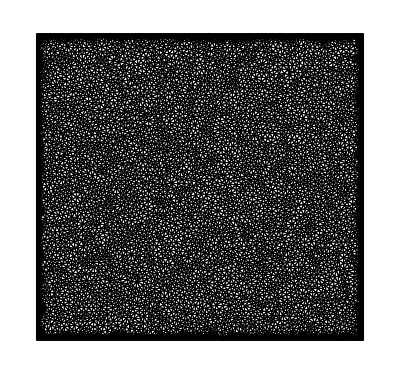

```mathematica
icPos =Transpose[{Table[xt0, 25], yt0}]
icVar ={{deltaVar, 0},{0, deltaVar}}
ic0 = N[Table[PDF[MultinormalDistribution[pos,icVar], {xt, yt}], {pos, icPos}]];
Sqrt[icVar]
bcFunc[xtl_, xtr_, ytl_, ytr_] :={
	  p[t, xtl, yt]==0,
           p[t, xtr, yt]==0,
           p[t, xt, ytr]==0,
           p[t, xt, ytl]==0
};
ΩFunc[xtl_, xtr_, ytl_, ytr_] :=ImplicitRegion[True,{{xt,xtl,xtr},{yt,ytl,ytr}}];
bcs = MapThread[bcFunc, {xtls, xtrs, ytls, ytrs}];
Ω=MapThread[ΩFunc,{xtls, xtrs, ytls, ytrs}]
meshes = Table[ToElementMesh[o, MaxCellMeasure->minCell, MaxBoundaryCellMeasure->minCell/4], {o, Ω}]
meshes[[1]]["Wireframe"]
```

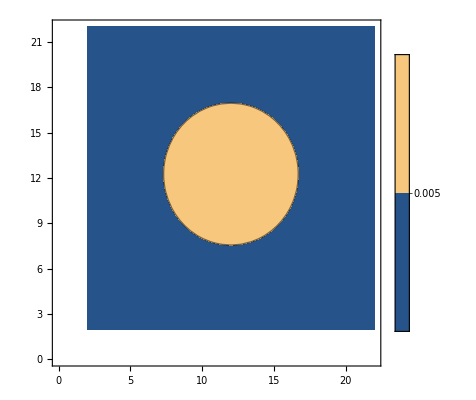

```mathematica
toPlot=1;
ContourPlot[ic0[[toPlot]], {xt, xt0-10, xt0+10}, {yt, xt0-10, xt0+10}, PlotRange->{0,0.05}, PlotLegends->Automatic]
```

## Calculate the time-integrated probability distribution and the flux through the boundary

```mathematica
NDSolverParams[param_, ic_, bc_, reg_, tf_] :=Module[{N},
N = NDSolve[Join[{(FP/. param),p[0, xt,yt]== ic}, bc],
                                   p,{t, 0, tf},{xt, yt}∈reg, 
Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement"}}}];
Return[(p/.N[[1]])];
]
```

```mathematica
solsIc0=MapThread[NDSolverParams, {params, ic0, bcs, meshes, tfs}];
```

NDSolve::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

$Aborted

```mathematica
dv = Table[Derivative[0,0,1][sol], {sol, solsIc0}];
```

```mathematica
Manipulate[Plot3D[solsIc0[[25]][t, xt, yt], {xt, 0,xtrs[[5]]}, {yt, 0,ytrs[[25]]}, AxesLabel->{xt, yt}, PlotRange->{-0.01, 0.3}, PlotLegends->Automatic, PerformanceGoal->"Quality"],{t, 0, tfs[[25]]}]
```

xtls gives the “left” boundary in x as 5 stds of the ss distribution from 0. To get the hitting distribution, integrate from there to 0+5*std

```mathematica
xranges = MapThread[N[Range[#1, #2, (#2-#1)/50]]&,{xtls, Table[3, 25]}]
```

{{-0.5,-0.43,-0.36,-0.29,-0.22,-0.15,-0.08,-0.01,0.06,0.13,0.2,0.27,0.34,0.41,0.48,0.55,0.62,0.69,0.76,0.83,0.9,0.97,1.04,1.11,1.18,1.25,1.32,1.39,1.46,1.53,1.6,1.67,1.74,1.81,1.88,1.95,2.02,2.09,2.16,2.23,2.3,2.37,2.44,2.51,2.58,2.65,2.72,2.79,2.86,2.93,3.},{-1.,-0.92,-0.84,-0.76,-0.68,-0.6,-0.52,-0.44,-0.36,-0.28,-0.2,-0.12,-0.04,0.04,0.12,0.2,0.28,0.36,0.44,0.52,0.6,0.68,0.76,0.84,0.92,1.,1.08,1.16,1.24,1.32,1.4,1.48,1.56,1.64,1.72,1.8,1.88,1.96,2.04,2.12,2.2,2.28,2.36,2.44,2.52,2.6,2.68,2.76,2.84,2.92,3.},{-1.5,-1.41,-1.32,-1.23,-1.14,-1.05,-0.96,-0.87,-0.78,-0.69,-0.6,-0.51,-0.42,-0.33,-0.24,-0.15,-0.06,0.03,0.12,0.21,0.3,0.39,0.48,0.57,0.66,0.75,0.84,0.93,1.02,1.11,1.2,1.29,1.38,1.47,1.56,1.65,1.74,1.83,1.92,2.01,2.1,2.19,2.28,2.37,2.46,2.55,2.64,2.73,2.82,2.91,3.},{-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.},{-2.5,-2.39,-2.28,-2.17,-2.06,-1.95,-1.84,-1.73,-1.62,-1.51,-1.4,-1.29,-1.18,-1.07,-0.96,-0.85,-0.74,-0.63,-0.52,-0.41,-0.3,-0.19,-0.08,0.03,0.14,0.25,0.36,0.47,0.58,0.69,0.8,0.91,1.02,1.13,1.24,1.35,1.46,1.57,1.68,1.79,1.9,2.01,2.12,2.23,2.34,2.45,2.56,2.67,2.78,2.89,3.},{-0.5,-0.43,-0.36,-0.29,-0.22,-0.15,-0.08,-0.01,0.06,0.13,0.2,0.27,0.34,0.41,0.48,0.55,0.62,0.69,0.76,0.83,0.9,0.97,1.04,1.11,1.18,1.25,1.32,1.39,1.46,1.53,1.6,1.67,1.74,1.81,1.88,1.95,2.02,2.09,2.16,2.23,2.3,2.37,2.44,2.51,2.58,2.65,2.72,2.79,2.86,2.93,3.},{-1.,-0.92,-0.84,-0.76,-0.68,-0.6,-0.52,-0.44,-0.36,-0.28,-0.2,-0.12,-0.04,0.04,0.12,0.2,0.28,0.36,0.44,0.52,0.6,0.68,0.76,0.84,0.92,1.,1.08,1.16,1.24,1.32,1.4,1.48,1.56,1.64,1.72,1.8,1.88,1.96,2.04,2.12,2.2,2.28,2.36,2.44,2.52,2.6,2.68,2.76,2.84,2.92,3.},{-1.5,-1.41,-1.32,-1.23,-1.14,-1.05,-0.96,-0.87,-0.78,-0.69,-0.6,-0.51,-0.42,-0.33,-0.24,-0.15,-0.06,0.03,0.12,0.21,0.3,0.39,0.48,0.57,0.66,0.75,0.84,0.93,1.02,1.11,1.2,1.29,1.38,1.47,1.56,1.65,1.74,1.83,1.92,2.01,2.1,2.19,2.28,2.37,2.46,2.55,2.64,2.73,2.82,2.91,3.},{-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.},{-2.5,-2.39,-2.28,-2.17,-2.06,-1.95,-1.84,-1.73,-1.62,-1.51,-1.4,-1.29,-1.18,-1.07,-0.96,-0.85,-0.74,-0.63,-0.52,-0.41,-0.3,-0.19,-0.08,0.03,0.14,0.25,0.36,0.47,0.58,0.69,0.8,0.91,1.02,1.13,1.24,1.35,1.46,1.57,1.68,1.79,1.9,2.01,2.12,2.23,2.34,2.45,2.56,2.67,2.78,2.89,3.},{-0.5,-0.43,-0.36,-0.29,-0.22,-0.15,-0.08,-0.01,0.06,0.13,0.2,0.27,0.34,0.41,0.48,0.55,0.62,0.69,0.76,0.83,0.9,0.97,1.04,1.11,1.18,1.25,1.32,1.39,1.46,1.53,1.6,1.67,1.74,1.81,1.88,1.95,2.02,2.09,2.16,2.23,2.3,2.37,2.44,2.51,2.58,2.65,2.72,2.79,2.86,2.93,3.},{-1.,-0.92,-0.84,-0.76,-0.68,-0.6,-0.52,-0.44,-0.36,-0.28,-0.2,-0.12,-0.04,0.04,0.12,0.2,0.28,0.36,0.44,0.52,0.6,0.68,0.76,0.84,0.92,1.,1.08,1.16,1.24,1.32,1.4,1.48,1.56,1.64,1.72,1.8,1.88,1.96,2.04,2.12,2.2,2.28,2.36,2.44,2.52,2.6,2.68,2.76,2.84,2.92,3.},{-1.5,-1.41,-1.32,-1.23,-1.14,-1.05,-0.96,-0.87,-0.78,-0.69,-0.6,-0.51,-0.42,-0.33,-0.24,-0.15,-0.06,0.03,0.12,0.21,0.3,0.39,0.48,0.57,0.66,0.75,0.84,0.93,1.02,1.11,1.2,1.29,1.38,1.47,1.56,1.65,1.74,1.83,1.92,2.01,2.1,2.19,2.28,2.37,2.46,2.55,2.64,2.73,2.82,2.91,3.},{-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.},{-2.5,-2.39,-2.28,-2.17,-2.06,-1.95,-1.84,-1.73,-1.62,-1.51,-1.4,-1.29,-1.18,-1.07,-0.96,-0.85,-0.74,-0.63,-0.52,-0.41,-0.3,-0.19,-0.08,0.03,0.14,0.25,0.36,0.47,0.58,0.69,0.8,0.91,1.02,1.13,1.24,1.35,1.46,1.57,1.68,1.79,1.9,2.01,2.12,2.23,2.34,2.45,2.56,2.67,2.78,2.89,3.},{-0.5,-0.43,-0.36,-0.29,-0.22,-0.15,-0.08,-0.01,0.06,0.13,0.2,0.27,0.34,0.41,0.48,0.55,0.62,0.69,0.76,0.83,0.9,0.97,1.04,1.11,1.18,1.25,1.32,1.39,1.46,1.53,1.6,1.67,1.74,1.81,1.88,1.95,2.02,2.09,2.16,2.23,2.3,2.37,2.44,2.51,2.58,2.65,2.72,2.79,2.86,2.93,3.},{-1.,-0.92,-0.84,-0.76,-0.68,-0.6,-0.52,-0.44,-0.36,-0.28,-0.2,-0.12,-0.04,0.04,0.12,0.2,0.28,0.36,0.44,0.52,0.6,0.68,0.76,0.84,0.92,1.,1.08,1.16,1.24,1.32,1.4,1.48,1.56,1.64,1.72,1.8,1.88,1.96,2.04,2.12,2.2,2.28,2.36,2.44,2.52,2.6,2.68,2.76,2.84,2.92,3.},{-1.5,-1.41,-1.32,-1.23,-1.14,-1.05,-0.96,-0.87,-0.78,-0.69,-0.6,-0.51,-0.42,-0.33,-0.24,-0.15,-0.06,0.03,0.12,0.21,0.3,0.39,0.48,0.57,0.66,0.75,0.84,0.93,1.02,1.11,1.2,1.29,1.38,1.47,1.56,1.65,1.74,1.83,1.92,2.01,2.1,2.19,2.28,2.37,2.46,2.55,2.64,2.73,2.82,2.91,3.},{-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.},{-2.5,-2.39,-2.28,-2.17,-2.06,-1.95,-1.84,-1.73,-1.62,-1.51,-1.4,-1.29,-1.18,-1.07,-0.96,-0.85,-0.74,-0.63,-0.52,-0.41,-0.3,-0.19,-0.08,0.03,0.14,0.25,0.36,0.47,0.58,0.69,0.8,0.91,1.02,1.13,1.24,1.35,1.46,1.57,1.68,1.79,1.9,2.01,2.12,2.23,2.34,2.45,2.56,2.67,2.78,2.89,3.},{-0.5,-0.43,-0.36,-0.29,-0.22,-0.15,-0.08,-0.01,0.06,0.13,0.2,0.27,0.34,0.41,0.48,0.55,0.62,0.69,0.76,0.83,0.9,0.97,1.04,1.11,1.18,1.25,1.32,1.39,1.46,1.53,1.6,1.67,1.74,1.81,1.88,1.95,2.02,2.09,2.16,2.23,2.3,2.37,2.44,2.51,2.58,2.65,2.72,2.79,2.86,2.93,3.},{-1.,-0.92,-0.84,-0.76,-0.68,-0.6,-0.52,-0.44,-0.36,-0.28,-0.2,-0.12,-0.04,0.04,0.12,0.2,0.28,0.36,0.44,0.52,0.6,0.68,0.76,0.84,0.92,1.,1.08,1.16,1.24,1.32,1.4,1.48,1.56,1.64,1.72,1.8,1.88,1.96,2.04,2.12,2.2,2.28,2.36,2.44,2.52,2.6,2.68,2.76,2.84,2.92,3.},{-1.5,-1.41,-1.32,-1.23,-1.14,-1.05,-0.96,-0.87,-0.78,-0.69,-0.6,-0.51,-0.42,-0.33,-0.24,-0.15,-0.06,0.03,0.12,0.21,0.3,0.39,0.48,0.57,0.66,0.75,0.84,0.93,1.02,1.11,1.2,1.29,1.38,1.47,1.56,1.65,1.74,1.83,1.92,2.01,2.1,2.19,2.28,2.37,2.46,2.55,2.64,2.73,2.82,2.91,3.},{-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.},{-2.5,-2.39,-2.28,-2.17,-2.06,-1.95,-1.84,-1.73,-1.62,-1.51,-1.4,-1.29,-1.18,-1.07,-0.96,-0.85,-0.74,-0.63,-0.52,-0.41,-0.3,-0.19,-0.08,0.03,0.14,0.25,0.36,0.47,0.58,0.69,0.8,0.91,1.02,1.13,1.24,1.35,1.46,1.57,1.68,1.79,1.9,2.01,2.12,2.23,2.34,2.45,2.56,2.67,2.78,2.89,3.}}

```mathematica
nintxsolve[xr_, s_, tf_, ystar_]:=Module[{t, x, f},
n =Table[NDSolveValue[{g'[t]==s[t, x, ystar],g[0]==0},g,{t, 0, tf},Method->{"ExplicitRungeKutta", "DifferenceOrder"->4}][tf], {x, xr}];
Return[n];
];
```

```mathematica
toIntegrate[t] = dv[[1]][t, 1, cstar[[1]]]
```

InterpolatingFunction[{{0., 250.}, {-0.5, 19.5761}, {1.02084, 19.8247}}, <>][t,1,1.02084]

```mathematica
NDSolveValue[{g'[t]==toIntegrate[t],g[0]==0},g,{t, 0, 250}, Method->Automatic][250]//AbsoluteTiming
```

{0.74652,29.5321}

```mathematica
NDSolveValue[{g'[t]==toIntegrate[t],g[0]==0},g,{t, 0, 250}, Method->{"ExplicitRungeKutta", "DifferenceOrder"->4}][250]//AbsoluteTiming
```

{0.733717,29.5321}

```mathematica
NDSolveValue[{g'[t]==toIntegrate[t],g[0]==0},g,{t, 0, 250}, Method->{"Extrapolation"}][250]//AbsoluteTiming
```

{0.765586,29.5322}

```mathematica
xvals = MapThread[nintxsolve, {xranges, dv, tfs, cstar}];
```

```mathematica
X=MapThread[Interpolation[Transpose@{#1, #2}][x]&, {xranges, xvals*αArray2/2}];
```

InterpolatingFunction::dmval: Input value {-0.999918} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

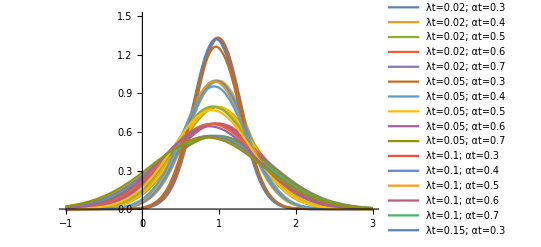

```mathematica
Plot[X, {x, -1, 3}, PlotLegends->legend, PlotRange->{-0.1, 1.5}]
```

```mathematica
bounds = Table[y[[0]][[1]][[1]], {y, X}]
```

{{-0.5,3.},{-1.,3.},{-1.5,3.},{-2.,3.},{-2.5,3.},{-0.5,3.},{-1.,3.},{-1.5,3.},{-2.,3.},{-2.5,3.},{-0.5,3.},{-1.,3.},{-1.5,3.},{-2.,3.},{-2.5,3.},{-0.5,3.},{-1.,3.},{-1.5,3.},{-2.,3.},{-2.5,3.},{-0.5,3.},{-1.,3.},{-1.5,3.},{-2.,3.},{-2.5,3.}}

```mathematica
IntegFunc[f_, bound_] :=NIntegrate[f, {x, bound[[1]], bound[[2]]}]
```

```mathematica
X[[1]]
```

InterpolatingFunction[…][x]

```mathematica
normsIc0 = MapThread[IntegFunc, {X,bounds}]
corrected = MapThread[#1/#2&, {X, normsIc0}];
meansIc0= MapThread[IntegFunc, {corrected*x,bounds}]
secondIc0 = MapThread[IntegFunc, {corrected*x*x,bounds}]
varsIc0 = secondIc0-meansIc0^2
diffIc0 = varsIc0/meansIc0^2;
```

{0.99884,1.00237,0.99498,1.00095,0.99769,1.00345,0.995386,0.99887,1.00014,0.991531,0.997625,1.00289,0.998315,1.0005,1.00187,0.998613,1.00102,1.00334,1.00034,0.999031,0.994292,0.998636,1.00131,1.00108,1.00559}

{0.992063,0.989133,0.986219,0.982627,0.976181,0.981367,0.97421,0.96699,0.959153,0.948881,0.967527,0.95334,0.938952,0.92395,0.906992,0.958668,0.937988,0.916509,0.894317,0.870072,0.961671,0.934356,0.903606,0.869549,0.832544}

{1.07396,1.13828,1.22239,1.32389,1.43397,1.05294,1.10902,1.18492,1.2785,1.38243,1.02618,1.06904,1.13188,1.21299,1.30652,1.00967,1.04084,1.09144,1.16085,1.24373,1.02362,1.04662,1.08519,1.13908,1.2062}

{0.0897717,0.159893,0.249766,0.358329,0.481038,0.0898599,0.159933,0.249849,0.358529,0.482053,0.0900737,0.160179,0.250252,0.359303,0.483883,0.0906218,0.161018,0.251451,0.361048,0.486701,0.0988066,0.1736,0.268686,0.38296,0.513066}

```mathematica
grid = Flatten[Table[{l, a}, {l, λts}, {a, αts}], 1];
params
```

{{λt→0.02,αt→0.3},{λt→0.02,αt→0.4},{λt→0.02,αt→0.5},{λt→0.02,αt→0.6},{λt→0.02,αt→0.7},{λt→0.05,αt→0.3},{λt→0.05,αt→0.4},{λt→0.05,αt→0.5},{λt→0.05,αt→0.6},{λt→0.05,αt→0.7},{λt→0.1,αt→0.3},{λt→0.1,αt→0.4},{λt→0.1,αt→0.5},{λt→0.1,αt→0.6},{λt→0.1,αt→0.7},{λt→0.15,αt→0.3},{λt→0.15,αt→0.4},{λt→0.15,αt→0.5},{λt→0.15,αt→0.6},{λt→0.15,αt→0.7},{λt→0.24,αt→0.3},{λt→0.24,αt→0.4},{λt→0.24,αt→0.5},{λt→0.24,αt→0.6},{λt→0.24,αt→0.7}}

```mathematica
normArrayIc0 = ArrayReshape[normsIc0, {5,5}];
varArrayIc0 = ArrayReshape[varsIc0, {5,5}];
meanArrayIc0 = ArrayReshape[meansIc0, {5,5}];
diffArrayIc0 = ArrayReshape[diffIc0,{5,5}];
```

```mathematica
cf[x_]:=Blend[{{0, Red},{ 1,White},{2,Blue}}, x]
xticks = Transpose[{{1, 2, 3, 4, 5}, λts}];
yticks = Transpose[{{1, 2, 3, 4, 5}, αts}];
```

```mathematica
ArrayPlot[varArrayIc0, ColorFunction->(Blend[{{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"Var("ϵ(OverTilde[x])   .")"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, αt}]
Grid[N[Reverse[varArrayIc0],5]]
Grid[N[Reverse[normArrayIc0],5]]
```

-Graphics-

0.100666 | 0.175874 | 0.271421 | 0.387182 | 0.522664
0.0906011 | 0.161031 | 0.251529 | 0.362069 | 0.492148
0.0901024 | 0.160196 | 0.250335 | 0.360463 | 0.489989
0.0898663 | 0.15993 | 0.249962 | 0.35993 | 0.489112
0.0896755 | 0.159891 | 0.249907 | 0.359928 | 0.488809

0.979887 | 0.996844 | 0.999037 | 0.999489 | 0.999598
0.995877 | 0.999624 | 0.99985 | 0.999902 | 0.99985
0.999248 | 0.999923 | 0.99995 | 0.999959 | 0.999867
0.999834 | 0.999995 | 0.999985 | 0.999976 | 0.999859
0.999986 | 1.00001 | 1. | 0.999976 | 0.999833

```mathematica
(.1-.0897)/.0897
```

0.114827

```mathematica
(.5227-.4888)/.4888
```

0.0693535

```mathematica
ArrayPlot[ArrayReshape[Table[Blend[{{0, Red},{ 1,White},{5,Blue}}, i],{i,Flatten[meanArrayIc0]}], {5,5}], PlotLegends->{Placed[BarLegend[{cf[#]&,{0, 5}},LegendLabel->"mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, αt}]
Grid[N[Reverse[meanArrayIc0],4]]
```

-Graphics-

0.953646 | 0.926393 | 0.895558 | 0.862296 | 0.827177
0.958666 | 0.937853 | 0.916492 | 0.894821 | 0.872722
0.967488 | 0.953291 | 0.938995 | 0.924615 | 0.909973
0.98146 | 0.974194 | 0.96706 | 0.959912 | 0.952429
0.992054 | 0.989099 | 0.986275 | 0.983456 | 0.980137

```mathematica
ArrayPlot[diffArrayIc0, ColorFunction->(Blend[{{ 0,White},{3,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"varScaledToMean2(e(x))"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, αt}]
Grid[N[Reverse[diffArrayIc0],4]]
```

-Graphics-

0.11069 | 0.204932 | 0.33842 | 0.520717 | 0.763881
0.0985821 | 0.18308 | 0.299454 | 0.452187 | 0.646166
0.0962598 | 0.176279 | 0.283919 | 0.421637 | 0.591739
0.0932936 | 0.168515 | 0.26728 | 0.39062 | 0.539192
0.0911179 | 0.163434 | 0.25691 | 0.372139 | 0.508822